```mathematica
OldStepIterate[]:=Block[{},
(* Iteration procedure *)
Iterate:=Block[{},
mPrint["Numerical iterations towards Λ=",Λtarget];
mPrint["If step becomes below 10^-7, try to increase prec"];
pp=pmin;qq=1;
step:=qq/base^pp;
(* starting the procedure *)
ΛLast=Λvals[[-1]];
Monitor[
While[ΛLast>Λtarget,
Λnew=Max[ΛLast-step,Λtarget];
normedrel=InterpEqns[Λnew];
Which[
Catch[SilentFindSol]==="Too big step",
pp=pp+1,
i>5,
sol[Λnew]=minsolrep;
AppendTo[Λvals,Λnew]
,
True,
sol[Λnew]=minsolrep;
AppendTo[Λvals,Λnew];
If[pp>pmin,qq=qq+Δq;If[qq==base,qq=1;pp=pp-1]];
];
ΛLast=Λvals[[-1]]
],
Row@{"Current Λ is: ",ΛLast//N,"   step is: ",step//N}]//PrintDone;
mPrint["Finished iterations. List of all Λ computed: ", Λvals//N];
];
]

(*0.5 and 7 is good*)
NewStepIterate[howcloselambda1_,smalllambda_]:=Block[{},
Iterate:=Block[{},
mPrint["Numerical iterations towards Λ=",Λtarget];
mPrint["If step becomes below 10^-7, try to increase prec"];
pp=pmin;qq=1;
step:=Module[{baseStep},baseStep=qq/base^pp;
If[ΛLast-Λtarget<=howcloselambda1,baseStep/smalllambda,(*reduce step if very close to the target*)baseStep]];
(* starting the procedure *)
ΛLast=Λvals[[-1]];
Monitor[
While[ΛLast>Λtarget,
Λnew=Max[ΛLast-step,Λtarget];
normedrel=InterpEqns[Λnew];
Which[
Catch[SilentFindSol]==="Too big step",
pp=pp+1,
i>5,
sol[Λnew]=minsolrep;
AppendTo[Λvals,Λnew]
,
True,
sol[Λnew]=minsolrep;
AppendTo[Λvals,Λnew];
If[pp>pmin,qq=qq+Δq;If[qq==base,qq=1;pp=pp-1]];
];
ΛLast=Λvals[[-1]]
],
Row@{"Current Λ is: ",ΛLast//N,"   step is: ",step//N}]//PrintDone;
mPrint["Finished iterations. List of all Λ computed: ", Λvals//N];
]
]

parameter[vprec_]:=Block[{},
maxord=5; (* Number of orders in analytic 1/Λ expansion of large θ solution. Generation of each next order is time-costly.  Roughly, the lower maxord is the bigger Λ0 is needed *)
Λ0=4; (* use analytic expressions as a solution guess for Λ≥Λ0. Large Λ may need larger prec. May need Λ0=4 for big systems *)
prec=vprec; (* Precision to use in computations. If iteration step drops below 10^-6, try increasing precision. Until length 16 prec=40 should be ok, then need prec=80 sometimes. After length 20, need play more seriously with prec *)
interpord=40; (* how many points from previous computations to take to guess the next step. Seriously affects convergence speed. Good values are between approx. 20 and 40 and depend on solution. *)
startinterpord=15; (* how many points to generate from asymptotic solution *)
$MaxPrecision=Infinity;(* I don't remember why I neded this. Maybe already irrelevant *)
MyMaxIterations=15; (* Number of iterations before aborting attempts to converge. *) 
base=2;pmin=3;RecoverySpeed=1/100000;
Δq=(base-1)Min[1,RecoverySpeed];
(* step of iteration is computed as q/base^p and it is automatically adjusted: q->q+Δq if converges fast; p->p+1 if computation aborts; q->1,p->p-1 if q=base *)
(* increase base and/or pmin if you want to reduce maximal allowed step *)
Λtarget=1; (* when to terminate iteration *)]
```

```mathematica
FindDuplicateRootPositions[solvedBetheroots_]:=Module[{roundedBetheRoots
,tallyBetheRoots,rootMultiplicity,duplicatePositions,duplicateRoots,duplicateRootPositions,duplicateRootPositionsFlatten},
roundedBetheRoots = Round[solvedBetheroots[[All, 1]], 10^-5]; (* Round Bethe roots to 5 decimal places *)
tallyBetheRoots = Tally[roundedBetheRoots]; (* Count occurrences of each rounded root *)
rootMultiplicity = tallyBetheRoots[[All, 2]]; (* Extract multiplicities *)
duplicatePositions = 
  Flatten[Position[rootMultiplicity, x_ /; x != 1]]; (* Identify positions where multiplicity ≠ 1 *)
duplicateRoots = Table[tallyBetheRoots[[All, 1]][[k]], {k, duplicatePositions}]; (* Extract duplicate roots *)
duplicateRootPositions = Table[
   Position[roundedBetheRoots, duplicateRoots[[k]]], 
   {k, Length[duplicateRoots]}
] ;(* Find positions of duplicate roots in original list *)
duplicateRootPositionsFlatten=Flatten[#,1]&/@duplicateRootPositions

]
```

```mathematica
lazySolver[yd_, riggs_, maxTime_: 5, maxRetries_: 2] := 
 Module[{L, rigs, mySYT, attempt, result},
  parameter[20];
  L = Total[yd];
  rigs = ModestoRiggedConfig[L, #] & /@ ModesConfig[yd];
  mySYT = ToSYT /@ rigs;
  
  Print[riggs];
  
  (*time constraint *)
  attempt = 0;
  While[attempt < maxRetries, 
   attempt++;
   result = TimeConstrained[SolutionFromSYT[mySYT[[riggs]]], maxTime, $Failed];
   If[result =!= $Failed, Break[]]; (* If it succeeds, break the loop *)
  ];
  
  (* If all attempts failed, return None and riggs immediately *)
  If[result === $Failed,Return[None, riggs],
  
  (* Proceed only if SolutionFromSYT succeeded *)
  
  NotebookDelete[Cells[CellStyle -> "Print"]];
  
  Module[{allbetheQ, mysol, allbetherootEqns, solvedBetheroots, 
    listCcoefficient, listUmonomial, listUmonomialValue, 
    listUmonomialCoffValue},
   
   allbetheQ = {};
   mysol = 
    Table[YQa[a, 0], {a, Length[λ - 1]}] /. 
     First[vars2nvars /. {FindSol[[2]]} /. Λ -> 1];
   
   AppendTo[allbetheQ, mysol];
   
   allbetherootEqns = Map[# == 0 &, allbetheQ, {2}][[All, 1 ;; 2]];
   solvedBetheroots =
    (Table[
        Table[
         Solve[allbetherootEqns[[w]][[k]], u],
         {k, Length[allbetherootEqns[[w]]]}],
        {w, Length[allbetherootEqns]}] // Values) - 1;
   
   listCcoefficient = 
    Table[vars2nvars /. Λ -> Λvals[[k]] /. 
      sol[Λvals[[k]]], {k, 
      Length[Λvals]}];
   
   listUmonomial = 
    Table[{k, Λvals[[k]], 
      Table[YQa[a, 0], {a, Length[λ] - 1}]}, {k, 
      Length[Λvals]}];
   
   listUmonomialValue = 
    MapThread[
     ReplaceAll, {listUmonomial[[All, 3]], listCcoefficient}];
   
   listUmonomialCoffValue = CoefficientList[listUmonomialValue, u];
   
   {solvedBetheroots, listUmonomialCoffValue, Λvals}
   ]
]]
```

```mathematica
lazySolver[yd_, riggs_, maxTime_ : 40, maxRetries_ : 10] := 
  Module[{L, rigs, mySYT, attempt, result, paramValue},
    
     paramValue = 80; (* Initial value of parameter *)
    L = Total[yd];
    rigs = ModestoRiggedConfig[L, #] & /@ ModesConfig[yd];
    mySYT = ToSYT /@ rigs;
    
    Print[riggs];
    
    (* Retry loop with increasing parameter values *)
    attempt = 0;
    result = $Failed; (* Initialize result to failed state *)
    
    While[attempt < maxRetries && result === $Failed,
      
      Print["Current paramValue: ", paramValue];
      
      parameter[paramValue]; (* Set parameter value *)
      attempt++;
      
      result = 
        TimeConstrained[SolutionFromSYT[mySYT[[riggs]]]//Quiet, maxTime, $Failed];
        NotebookDelete[Cells[CellStyle -> "Print"]];
      (* If the result is successful, exit loop *)
      If[result =!= $Failed, Break[],paramValue += 20];
      
      (* Increase parameter only when SolutionFromSYT fails *)
      
    ];
    
    (* If all attempts failed, return None and riggs *)
    If[result === $Failed, Return[{None, riggs}],
     
     (* Proceed only if SolutionFromSYT succeeded *)
     
   
     
     Module[{allbetheQ, mysol, allbetherootEqns, solvedBetheroots, 
       listCcoefficient, listUmonomial, listUmonomialValue, 
       listUmonomialCoffValue},
       Print["succeeded with prec: " ,paramValue];
       allbetheQ = {};
       mysol = 
         Table[YQa[a, 0], {a, Length[λ - 1]}] /. 
           First[vars2nvars /. {FindSol[[2]]} /. Λ -> 1];
       
       AppendTo[allbetheQ, mysol];
       
       allbetherootEqns = Map[# == 0 &, allbetheQ, {2}][[All, 1 ;; 2]];
       solvedBetheroots =
         (Table[
                 Table[
                   Solve[allbetherootEqns[[w]][[k]], u],
                   {k, Length[allbetherootEqns[[w]]]}],
                 {w, Length[allbetherootEqns]}] // Values) - 1;
       
       listCcoefficient = 
         Table[vars2nvars /. Λ -> Λvals[[
          k]] /. 
             sol[Λvals[[k]]], {k, 
             Length[Λvals]}];
       
       listUmonomial = 
         Table[{k, Λvals[[k]], 
             Table[YQa[a, 0], {a, Length[λ] - 1}]}, {k, 
             Length[Λvals]}];
       
       listUmonomialValue = 
         MapThread[
           ReplaceAll, {listUmonomial[[All, 3]], listCcoefficient}];
       
       listUmonomialCoffValue = CoefficientList[listUmonomialValue, u];
       
       {solvedBetheroots, listUmonomialCoffValue, Λvals}
       ]
   ]]
```

```mathematica
sol1[[1]]
```

{{{{-0.7686206163655173},{-0.368687845900624-0.499628553590031 ⅈ},{-0.368687845900624+0.499628553590031 ⅈ}},{{-0.6357731010093056}}}}

```mathematica
sol1=lazySolver[yd,1,10,10];
```

17 succeeded with prec:

```mathematica
.b4
```

```mathematica
.
```

```mathematica
changeHistory={};
newlazysolver[yd_] := Module[{solvedBetheroots, duplicateRootPositions, 
   previousDuplicateRootPositions, iterationstep, newsolutions, changedPositions},
  OldStepIterate[];
  solvedBetheroots = ParallelTable[lazySolver[yd, rigg,50,2], {rigg, Length[rigs]}];
  NotebookDelete[Cells[CellStyle -> "Print"]]; (* Clear previous print outputs *)

  
  duplicateRootPositions = FindDuplicateRootPositions[solvedBetheroots]//Flatten;
 Print["Original dubbel" ,FindDuplicateRootPositions[solvedBetheroots]];
 previousDuplicateRootPositions = {}; (* Start with an empty comparison list *)

 
  iterationstep = 7;

  (* Iterate until there are no duplicate root positions *)
  While[duplicateRootPositions =!= {},
   
    (* Find positions that changed from the last iteration *)
    changedPositions = Complement[duplicateRootPositions, previousDuplicateRootPositions];

    (* Update only if any positions have changed *)
    If[changedPositions =!= {},
     AppendTo[changeHistory,changedPositions];
      (* Perform iteration step with increasing parameter *)
      NewStepIterate[0.3, iterationstep];
      iterationstep++; (* Increment iteration step *)

      (* Solve again only for the changed duplicate positions *)
      newsolutions = ParallelTable[
          lazySolver[yd, duplicateRootPositions[[position]],50,2],
          {position, Length[duplicateRootPositions]}];
   

      (* Update solvedBetheroots only for changed positions *)
      Do[
        solvedBetheroots[[duplicateRootPositions[[position]]]] = newsolutions[[ position]],
        {position, Length[duplicateRootPositions]}
      ];
,
    (* Update previous duplicate positions before next iteration *)
    previousDuplicateRootPositions = duplicateRootPositions;

    ];



    (* Update duplicate root positions based on the modified solvedBetheroots *)
    duplicateRootPositions = FindDuplicateRootPositions[solvedBetheroots]//Flatten;
  ];

  (* Return the updated set of solved roots *)
  solvedBetheroots
]
```

```mathematica
iterativLazysolver=newlazysolver[yd]
```

```mathematica
OldStepIterate[]
```

```mathematica
maxord=5; (* Number of orders in analytic 1/Λ expansion of large θ solution. Generation of each next order is time-costly.  Roughly, the lower maxord is the bigger Λ0 is needed *)
Λ0=4; (* use analytic expressions as a solution guess for Λ≥Λ0. Large Λ may need larger prec. May need Λ0=4 for big systems *)
prec=150; (* Precision to use in computations. If iteration step drops below 10^-6, try increasing precision. Until length 16 prec=40 should be ok, then need prec=80 sometimes. After length 20, need play more seriously with prec *)
interpord=40; (* how many points from previous computations to take to guess the next step. Seriously affects convergence speed. Good values are between approx. 20 and 40 and depend on solution. *)
startinterpord=15; (* how many points to generate from asymptotic solution *)
$MaxPrecision=Infinity;(* I don't remember why I neded this. Maybe already irrelevant *)
MyMaxIterations=15; (* Number of iterations before aborting attempts to converge. *) 
base=2;pmin=3;RecoverySpeed=1/10000;
Δq=(base-1)Min[1,RecoverySpeed];
(* step of iteration is computed as q/base^p and it is automatically adjusted: q->q+Δq if converges fast; p->p+1 if computation aborts; q->1,p->p-1 if q=base *)
(* increase base and/or pmin if you want to reduce maximal allowed step *)
Λtarget=1; (* when to terminate iteration *)
```

```mathematica
lazySolver[yd,3,30,1];
```

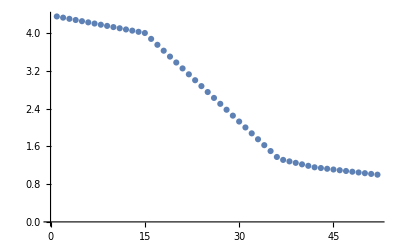

```mathematica
Λvals//ListPlot
```

```mathematica
SolutionFromSYT[mySYT[[1]]]
```

Set::shape: Lists {minim,minsolrep} and FindMinimum[normedrel.normedrel,Transpose[{nvars,nvars/.subnc}],WorkingPrecision→prec,PrecisionGoal→∞,AccuracyGoal→prec/2,MaxIterations→50,Method→Automatic,EvaluationMonitor:>(i++;If[i>MyMaxIterations,Throw[Too big step]])] are not the same shape.

$Aborted

```mathematica
Check[
  SolutionFromSYT[mySYT[[1]]], (* Expression to evaluate *)
  Break[], (* What to do if an error occurs *)
  {Set::shape} (* Specify message types if needed *)
]
```

Set::shape: Lists {minim,minsolrep} and FindMinimum[normedrel.normedrel,Transpose[{nvars,nvars/.subnc}],WorkingPrecision→prec,PrecisionGoal→∞,AccuracyGoal→prec/2,MaxIterations→50,Method→Automatic,EvaluationMonitor:>(i++;If[i>MyMaxIterations,Throw[Too big step]])] are not the same shape.

$Aborted

```mathematica
Check[
  A[[1, 2]] = 5,  (* This might cause Set::shape error *)
  "Error occurred"
]
```

Set::noval: Symbol A in part assignment does not have an immediate value.

Error occurred

```mathematica
While[True,
  If[FailureQ[Check[SolutionFromSYT[mySYT[[1]]], Failure]], 
     Break[] (* Stops execution if error occurs *)
  ]
]
```

Set::shape: Lists {minim,minsolrep} and FindMinimum[normedrel.normedrel,Transpose[{nvars,nvars/.subnc}],WorkingPrecision→prec,PrecisionGoal→∞,AccuracyGoal→prec/2,MaxIterations→50,Method→Automatic,EvaluationMonitor:>(i++;If[i>MyMaxIterations,Throw[Too big step]])] are not the same shape.

$Aborted